```mathematica
fun[x_]:=(x+3)*(x-1)*(x-1)
```

```mathematica
fun[1]
```

0

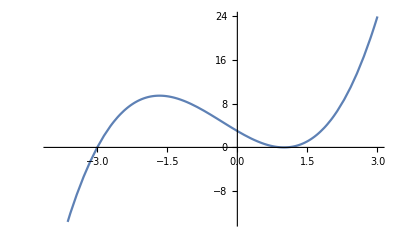

```mathematica
Plot[fun[x],{x,-4,3}]
```

```mathematica
s[a_,b_,c_]:=(((a*fun[b]*fun[c])/((fun[a]-fun[b])*(fun[a]-fun[c])))+((b*fun[a]*fun[c])/((fun[b]-fun[a])*(fun[b]-fun[c])))+((c*fun[b]*fun[b])/((fun[c]-fun[a])*(fun[c]-fun[b]))))
```

```mathematica
s[]
```

```mathematica
Sin[0.0000000000745474]
```

7.45474×10^-11